# 张量收缩图像

## 不同张量函数定义

```mathematica
textsize=50;
ratio = 1/5000;
thick =Thickness[textsize ratio];
equal[center_]:= Graphics[Text[Style["=",textsize],center]]
SqT[name_,center_,bond_]:=Graphics[{{EdgeForm[thick],
White,Rectangle[{center[[1]]-0.25,center[[2]]-0.25},{center[[1]]+0.25,center[[2]]+0.25}]},If[bond[[1]]==1,{thick,Line[{{center[[1]]-0.25,center[[2]]},{center[[1]]-0.5,center[[2]]}}]}],
If[bond[[2]]==1,{thick,Line[{{center[[1]],center[[2]]-0.25},{center[[1]],center[[2]]-0.5}}]}],
If[bond[[3]]==1,{thick,Line[{{center[[1]]+0.25,center[[2]]},{center[[1]]+0.5,center[[2]]}}]}],
If[bond[[4]]==1,{thick,Line[{{center[[1]],center[[2]]+0.25},{center[[1]],center[[2]]+0.5}}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
CiTL[name_,center_,bond_]:=Graphics[{{thick,Circle[center,0.25]},
If[bond[[1]]==1,{thick,Circle[{center[[1]]+0.25,center[[2]]-0.25},0.25,{Pi,3Pi/2}]}],
If[bond[[2]]==1,{thick,Circle[{center[[1]]+0.25,center[[2]]+0.25},0.25,{Pi/2,Pi}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
CiTR[name_,center_,bond_]:=Graphics[{{thick,Circle[center,0.25]},
If[bond[[1]]==1,{thick,Circle[{center[[1]]-0.25,center[[2]]-0.25},0.25,{3Pi/2,2Pi}]}],
If[bond[[2]]==1,{thick,Circle[{center[[1]]-0.25,center[[2]]+0.25},0.25,{0,Pi/2}]}],
Text[Style[name,textsize],center]},ImageSize->Medium]
```

## 作图

## 4

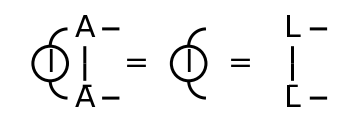

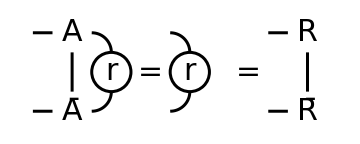

```mathematica
textsize =30;
thick =Thickness[textsize ratio];
Show[SqT[A,{0,0},{0,1,1,0}],SqT[Ā,{0,-1},{0,0,1,1}],CiTL[l,{-0.5,-0.5},{1,1}],
equal[{0.75,-0.5}],CiTL[l,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[L,{3,-0},{0,1,1,0}],SqT[L̄,{3,-1},{0,0,1,1}]]
Show[SqT[A,{0,0},{1,1,0,0}],SqT[Ā,{0,-1},{1,0,0,1}],CiTR[r,{0.5,-0.5},{1,1}],
equal[{1,-0.5}],CiTR[r,{1.5,-0.5},{1,1}],
equal[{2.25,-0.5}],SqT[R,{3,-0},{1,1,0,0}],SqT[R̄,{3,-1},{1,0,0,1}]]
```

## 5

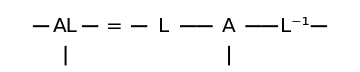

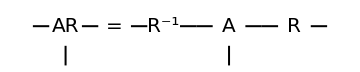

```mathematica
textsize =20;
thick =Thickness[textsize ratio];
Show[SqT[AL,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT[L,{1.5,0},{1,0,1,0}],SqT[A,{2.5,0},{1,1,1,0}],SqT["L^-1",{3.5,0},{1,0,1,0}]]
Show[SqT[AR,{0,0},{1,1,1,0}],
equal[{0.75,0}],SqT["R^-1",{1.5,0},{1,0,1,0}],SqT[A,{2.5,0},{1,1,1,0}],SqT[R,{3.5,0},{1,0,1,0}]]
```

## 7

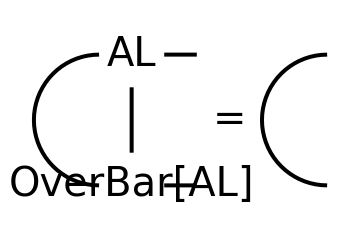
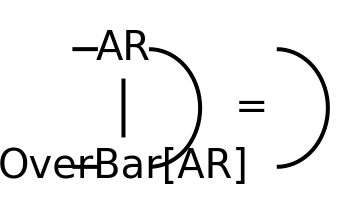

```mathematica
textsize =40;
thick =Thickness[textsize ratio];
{Show[SqT[AL,{0,0},{0,1,1,0}],SqT[OverBar[AL],{0,-1},{0,0,1,1}],Graphics[{thick,Circle[{-0.25,-0.5},0.5,{Pi/2,3Pi/2}]}],
equal[{0.75,-0.5}],Graphics[{thick,Circle[{1.5,-0.5},0.5,{Pi/2,3Pi/2}]}]],"                ",
Show[SqT[AR,{0,0},{1,1,0,0}],SqT[OverBar[AR],{0,-1},{1,0,0,1}],Graphics[{thick,Circle[{0.25,-0.5},0.5,{-Pi/2,Pi/2}]}],
equal[{1.25,-0.5}],Graphics[{thick,Circle[{1.5,-0.5},0.5,{-Pi/2,Pi/2}]}]]}
```